# NestedBranching

Generate a nested branching model

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
NestedBranching[b_, n_,OptionsPattern["Output"->"Graphic"]] :=
	Module[{nBranch,nestedPoints,lines},
		nBranch= Length[b];
		nestedPoints= NestList[Flatten[Outer[Times,1+#,b]]&,{0},n];
		lines=Flatten[MapIndexed[
			Table[
				Table[
					{#1[[x]],nestedPoints[[#2[[1]]+1]][[(x+(y-1)*Length[#1])]]},
					{y,nBranch}],
				{x,Length[#1]}]&,
			Most[nestedPoints]],2];
		If[
			OptionValue["Output"]=="Points",
			nestedPoints,
			If[
				OptionValue["Output"]=="EndPoints",
				Last[nestedPoints],
				If[
					OptionValue["Output"]=="Lines",
					lines,
					If[
						OptionValue["Output"]=="Graphic",
						Graphics[Line[Map[Reverse,ReIm[Join[{{-1,0}},lines]],2]]]]]]]]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

NestedBranching[b,n]

Generate a branching model of depth n specified by the rule b, a list of complex numbers representing the result of the first step.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

The "stem" of the model is assumed to be a line from -1 to 0.

The option "Output" defaults to "Graphic", can be used to determine the output format and accepts the following specifications:

"Graphics" | a visual representation of the model turned by 90° to face upwards
"Points" | a nested list representing the points at each layer
"EndPoints" | the endpoints of the model
"lines" | a list of list of length two representing the lines with no rotation or conversion from  complex numbers

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Get six layers of a branching model with two branches:

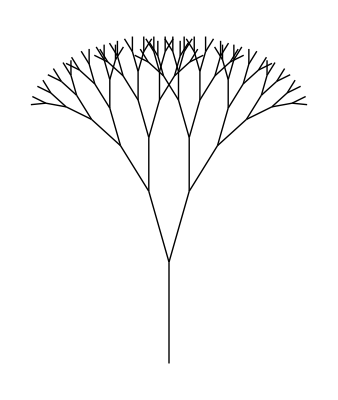

```mathematica
NestedBranching[{0.7+0.2I,0.7-0.2I},6]
```

### Scope

Retrieve the points instead of a graphic:

```mathematica
NestedBranching[{0.7+0.2I,0.7-0.2I},3,"Output"->"Points"]
```

{{0},{0.7+0.2 ⅈ,0.7-0.2 ⅈ},{1.15+0.48 ⅈ,1.23-0.2 ⅈ,1.23+0.2 ⅈ,1.15-0.48 ⅈ},{1.409+0.766 ⅈ,1.601-0.094 ⅈ,1.601+0.306 ⅈ,1.521-0.586 ⅈ,1.521+0.586 ⅈ,1.601-0.306 ⅈ,1.601+0.094 ⅈ,1.409-0.766 ⅈ}}

Visualize the points using ComplexListPlot:

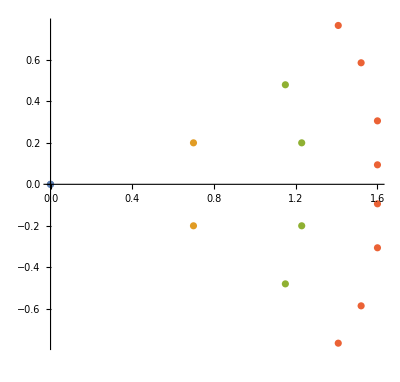

```mathematica
ComplexListPlot[NestedBranching[{0.7+0.2I,0.7-0.2I},3,"Output"->"Points"]]
```

The endpoints are just the last list in the points:

```mathematica
NestedBranching[{0.7+0.2I,0.7-0.2I},3,"Output"->"EndPoints"]
```

{1.409+0.766 ⅈ,1.601-0.094 ⅈ,1.601+0.306 ⅈ,1.521-0.586 ⅈ,1.521+0.586 ⅈ,1.601-0.306 ⅈ,1.601+0.094 ⅈ,1.409-0.766 ⅈ}

The lines can also be retrieved:

```mathematica
NestedBranching[{0.7+0.2I,0.7-0.2I},3,"Output"->"Lines"]
```

{{0,0.7+0.2 ⅈ},{0,0.7-0.2 ⅈ},{0.7+0.2 ⅈ,1.15+0.48 ⅈ},{0.7+0.2 ⅈ,1.23+0.2 ⅈ},{0.7-0.2 ⅈ,1.23-0.2 ⅈ},{0.7-0.2 ⅈ,1.15-0.48 ⅈ},{1.15+0.48 ⅈ,1.409+0.766 ⅈ},{1.15+0.48 ⅈ,1.521+0.586 ⅈ},{1.23-0.2 ⅈ,1.601-0.094 ⅈ},{1.23-0.2 ⅈ,1.601-0.306 ⅈ},{1.23+0.2 ⅈ,1.601+0.306 ⅈ},{1.23+0.2 ⅈ,1.601+0.094 ⅈ},{1.15-0.48 ⅈ,1.521-0.586 ⅈ},{1.15-0.48 ⅈ,1.409-0.766 ⅈ}}

The model works for any number of branches and does not have to be symmetric:

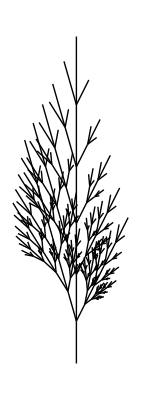

```mathematica
NestedBranching[{0.4+0.2I,1.1,0.7-0.2I},5]
```

### Neat Examples

A simple manipulate allows for the manual manipulation of the real and imaginary parts of each value in b:

```mathematica
Manipulate[NestedBranching[{Complex[a,b],Complex[c,-d]},depth],{{a,0.3,"Re[a]"},0,1},{{b,0.3,"Im[a]"},0,1},{{c,0.3,"Re[b]"},0,1},{{d,0.3,"Im[b]"},0,1},{{depth,7,"Depth"},1,10,1},SaveDefinitions->True]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Katja Della Libera

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

trees

leaves

fractals

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

NestList

ComplexListPlot

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://www.wolframscience.com/nks/notes-8-6--implementation-of-branching-model

https://www.wolframscience.com/nks/p400--growth-of-plants-and-animals/

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Greetings to everyone.